## The Mandelbrot Set F. I. Giasemis

### The Mandelbrot Set

```mathematica
MandelbrotSetPlot[]
```

-Graphics-

### Period-1

### Analytically

{{z→1/2 (1-√(1-4 c))},{z→1/2 (1+√(1-4 c))}}

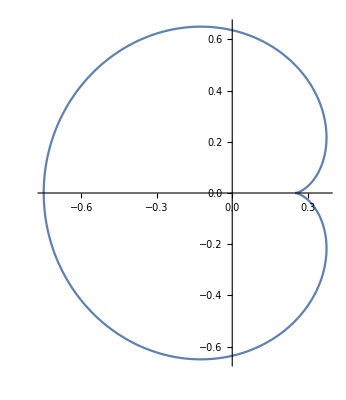

```mathematica
Solve[z^2-z+c==0,z]
c=Exp[I φ]/2-Exp[2 I φ]/4;
ParametricPlot[{Re[c],Im[c]},{φ,0,2π}]
```

### Numerically

```mathematica
sol=Solve[z^2-z+c==0,z]
```

{{z→ⅇ^(ⅈ φ)/2},{z→1/2 (2-ⅇ^(ⅈ φ))}}

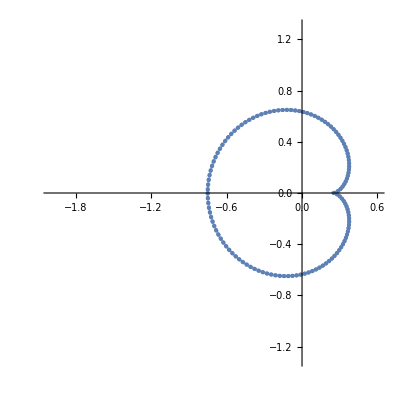

```mathematica
z1[c_]:=1/2 (1-√(1-4 c));
z2[c_]:=1/2 (1+√(1-4 c));
list={};
Quiet[
For[φ=0,φ<2π,φ+=0.05,
sol=NSolve[{2Abs[z1[r Exp[I φ]]]==1,r∈ Reals},r];
r1=r/.Part[sol,1,1];
r2=r/.Part[sol,2,1];
Z1=r1 Exp[I φ];
Z2=r2 Exp[I φ];
AppendTo[list,{Re[Z1],Im[Z1]}];
AppendTo[list,{Re[Z2],Im[Z2]}];
]
]
ListPlot[list,AspectRatio->1,PlotRange->{{-2,0.6},{-1.3,1.3}}]
```

### Period-2

### Numerically

```mathematica
Solve[z^4+2c z^2-z+c^2+c==0,z]
```

{{z→-0.500001+1.00004 ⅈ},{z→-0.499999-1.00004 ⅈ},{z→0.499929+0.00840695 ⅈ},{z→0.500071-0.00840695 ⅈ}}

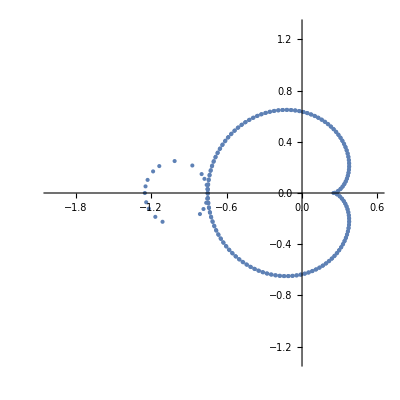

```mathematica
z1[c_]:=1/2 (-1-√(-3-4 c));
z2[c_]:=1/2 (-1+√(-3-4 c));
z3[c_]:=1/2 (1-√(1-4 c));
z4[c_]:=1/2 (1+√(1-4 c));
Quiet[
For[φ=0,φ<2π,φ+=0.1,
sol=NSolve[{Abs[4 z1[r Exp[I φ]]^3+4 (r Exp[I φ]) z1[r Exp[I φ]]]==1,r∈ Reals},r];
If[Length[sol]>0,
r1=r/.Part[sol,1,1];
r2=r/.Part[sol,2,1];
Z1=r1 Exp[I φ];
Z2=r2 Exp[I φ];
AppendTo[list,{Re[Z1],Im[Z1]}];
AppendTo[list,{Re[Z2],Im[Z2]}];
]
]
]
ListPlot[list,AspectRatio->1,PlotRange->{{-2,0.6},{-1.3,1.3}}]
```